#### Preamble

```mathematica
SetDirectory[NotebookDirectory[]]
<<"/home/juanathan/Documents/Wolfram Mathematica/Wolfram_scripts/Optics_ThinFilm.wls"
<<"~/Documents/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
```

/home/juanathan/Documents/Wolfram Mathematica/Wolfram_scripts

```mathematica
fs = 9;
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
graphsOpts:= {Mesh-> Full,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> ColorData[3]}
SetOptions[ListLinePlot,graphsOpts];
```

## Pruebas

### Fresnel Limits

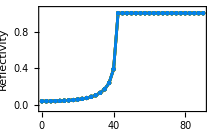
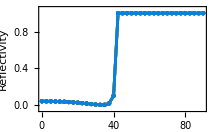

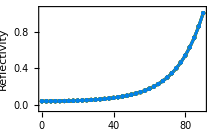
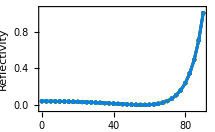

```mathematica
a = 25; b = 20;
lda = Range[500,600,20.];
ang = Range[0,90.,2.5]*Pi/180;
cfrac = 0.0;

epsilon = Transpose[Table[{1.,1.,1.5}^2,{lda}]];
data = norm2@ Map[Transpose[#[ang,epsilon,lda,{a,b},cfrac]]&, {ThinFilmReflectionS,ThinFilmReflectionP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Incidence angle [Deg]","Reflectivity"})]& /@ data
 
epsilon = Transpose[Table[{1.5,1.5,1.}^2,{lda}]];
data = norm2@ Map[Transpose[#[ang,epsilon,lda,{a,b},cfrac]]&, {ThinFilmReflectionS,ThinFilmReflectionP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Incidence angle [Deg]","Reflectivity"})]& /@ data
```

```mathematica
a = 25; b = 20;
lda = Range[500,600,20.];
ang = Range[0,90.,2.5]*Pi/180;
cfrac = 0.05;

epsilon = Transpose[Table[{1.,1.5,1.5}^2,{lda}]];
data = norm2@ Map[Transpose[#[ang,epsilon,lda,{a,b},cfrac]]&, {ThinFilmReflectionS,ThinFilmReflectionP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Wavelength [nm]","Reflectivity"})]& /@ data
 
epsilon = Transpose[Table[{1.5,1.,1.}^2,{lda}]];
data = norm2@ Map[Transpose[#[ang,epsilon,lda,{a,b},cfrac]]&, {ThinFilmReflectionS,ThinFilmReflectionP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Incidence angle [Deg]","Reflectivity"})]& /@ data
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{-Graphics-,-Graphics-}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{-Graphics-,-Graphics-}

### Gold Au

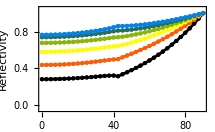
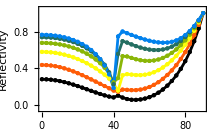

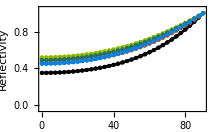
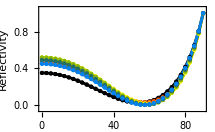

```mathematica
a = 5; b = 3;
lda = Range[500,600,20.];
ang = Range[0,90.,2.5]*Pi/180;
cfrac = 0.1;

epsilon = Transpose[Table[{1.,JohnsonChristyAuRef[i],1.5}^2,{i,lda}]];
data = norm2@ Map[Transpose[#[ang,epsilon,lda,{a,b},cfrac]]&, {ThinFilmReflectionS,ThinFilmReflectionP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Incidence angle [Deg]","Reflectivity"})]& /@ data
 
epsilon = Transpose[Table[{1.5,JohnsonChristyAuRef[i],1.}^2,{i,lda}]];
data = norm2@ Map[Transpose[#[ang,epsilon,lda,{a,b},cfrac]]&, {ThinFilmReflectionS,ThinFilmReflectionP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->ang[[{1,-1}]]*180/Pi,Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Incidence angle [Deg]","Reflectivity"})]& /@ data
```

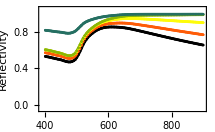
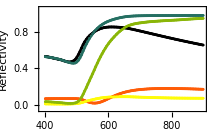

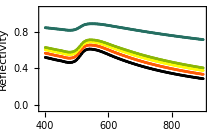
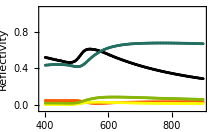

```mathematica
a = 4; b = 5;
lda = Range[400,900,5.];
ang = {0.,30.,40.,45.,75.}*Pi/180;
cfrac = 0.2;

epsilon = Transpose[Table[{1.,JohnsonChristyAuRef[i],1.5}^2,{i,lda}]];
data = norm2@ Map[#[ang,epsilon,lda,{a,b},cfrac]&, {ThinFilmReflectionS,ThinFilmReflectionP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->lda[[{1,-1}]],Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Wavelength [nm]","Reflectivity"})]& /@ data
 
epsilon = Transpose[Table[{1.5,JohnsonChristyAuRef[i],1.}^2,{i,lda}]];
data = norm2@ Map[#[ang,epsilon,lda,{a,b},cfrac]&, {ThinFilmReflectionS,ThinFilmReflectionP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->lda[[{1,-1}]],Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Wavelength [nm]","Reflectivity"})]& /@ data
```

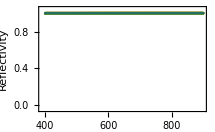
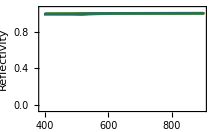

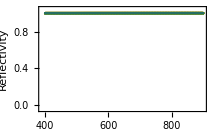
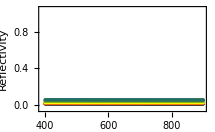

```mathematica
a = 50; b = 38;
lda = Range[400,900,5.];
ang = {65.,67.,69.,71.,73.}*Pi/180;
cfrac = 0.16;

epsilon = Transpose[Table[{1.33,JohnsonChristyAuRef[i],1.5}^2,{i,lda}]];
data = norm2@ Map[#[ang,epsilon,lda,{a,b},cfrac]&, {ThinFilmReflectionS,ThinFilmReflectionP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->lda[[{1,-1}]],Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Wavelength [nm]","Reflectivity"})]& /@ data
 
epsilon = Transpose[Table[{1.5,JohnsonChristyAuRef[i],1.33}^2,{i,lda}]];
data = norm2@ Map[#[ang,epsilon,lda,{a,b},cfrac]&, {ThinFilmReflectionS,ThinFilmReflectionP}];
ListLinePlot[#,PlotRange->{0-.05,1.05},DataRange->lda[[{1,-1}]],Evaluate[graphsOpts],
           FrameLabel->(Style[#,texStyle] &/@ {"Wavelength [nm]","Reflectivity"})]& /@ data
```